```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["SQLite"];
conn=OpenSQLConnection[JDBC["SQLite","/Users/erinhengel/Dropbox/Readability/dta/read.db"]];
font="Optima";
```

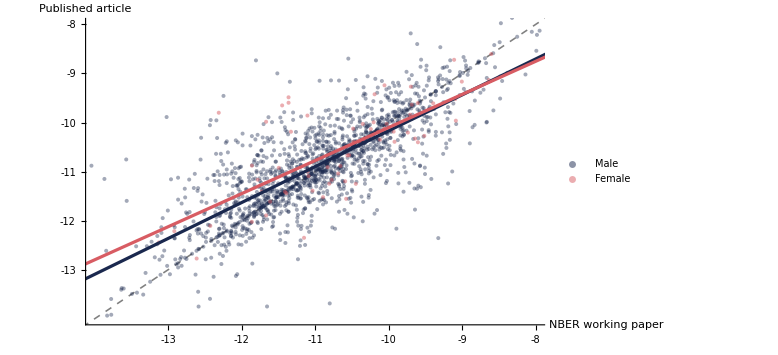

```mathematica
sql="SELECT FemRatio, -1 * StatValue AS _, nber_
		FROM NBERCorr
		NATURAL JOIN ReadStat
		NATURAL JOIN (
			SELECT ArticleID, 1 - AVG(Sex) AS FemRatio
				FROM Article
				NATURAL JOIN AuthorCorr
				NATURAL JOIN Author
			WHERE Language = 'English' AND Journal <> 'P&P'
			GROUP BY ArticleID
		) AS FemStat
		NATURAL JOIN (
			SELECT ArticleID, NberID, -1 * StatValue AS nber_
				FROM NBERCorr
				NATURAL JOIN NBERStat
			WHERE StatName = 'dalechall_score'
		) AS NberStat
	WHERE StatName = 'dalechall_score'
";
data=SQLExecute[conn,sql];
male=Select[data,#⟦1⟧==0&]⟦All,2;;⟧;
female=Select[data,#⟦1⟧==1&]⟦All,2;;⟧;

pointsize=PointSize[0.005];
thickness=Thickness[0.004];
{blue,pink}={RGBColor[26/255,40/255,78/255],RGBColor[216/255,92/255,99/255]};
legend=PointLegend[{blue,pink},{"Male","Female"},
LegendMarkers->Graphics[{EdgeForm[None],Opacity[0.5],Disk[]}],
LegendMarkerSize->10,
LabelStyle->{FontSize->12,FontColor->Gray,FontFamily->font},
LegendMargins->5,
LegendLayout->"Row"
];
MaleScatter=ListPlot[male,
PlotStyle->{blue,Opacity[0.4],pointsize}
];
MaleLine=Fit[male,{1,x},x];
MaleLinePlot=Plot[MaleLine,{x,Min@male⟦All,1⟧,Max@male⟦All,1⟧},
PlotStyle->{blue,thickness}
];
FemaleScatter=ListPlot[female,
PlotStyle->{pink,Opacity[0.5],pointsize},
PlotLegends->Placed[legend,{0.8,0.1}]
];
FemaleLine=Fit[female,{1,x},x];
FemaleLinePlot=Plot[FemaleLine,
{x,Min@male⟦All,1⟧,Max@male⟦All,1⟧},
PlotStyle->{{pink,thickness}, {pink,Dashing[Large],Opacity[0.5]}}
];
Line45=Plot[x,{x,Min@male⟦All,1⟧,Max@male⟦All,1⟧},
PlotStyle->{Gray,Thickness[0.002],Dashed}
];
plot=Show[{Line45,MaleScatter,FemaleScatter,MaleLinePlot,FemaleLinePlot},
AxesLabel->{"NBER\nworking paper","Published\narticle"},
PlotRange->{{-14,-8},{-14,-8}},
Axes->True,
Ticks->{{-13,-12,-11,-10,-9,-8},{-13,-12,-11,-10,-9,-8}},
ImageSize->Scaled[0.75],
AxesOrigin->Automatic,
AxesStyle->Directive[Thin,Gray,FontFamily->font,FontSize->Medium]
];
Export["/Users/erinhengel/Dropbox/Readability/draft/pdf/figure2.pdf",plot];
Show[plot,ImageSize->Large]
```